## Cosmological Perturbation Theory Package

First, load the package

```mathematica
<<COSPER`
```

Get::noopen: Cannot open "COSPER`".

$Failed

Brief on-line help is available for all functions:

```mathematica
?IMetric
```

IMetric[g], with g an n.n-matrix (two lower indices),
  returns the inverse metric (two upper indices).

```mathematica
Needs["PlotLegends`"]
SetDirectory["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\"]
```

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica

## Basic

### Background

First define the coordinate n-vector:

```mathematica
x={t,x1,x2,x3};
```

and then specify the metric as a square n×n matrix:

```mathematica
(met={{-a[t]*a[t],0,0,0},{0,a[t]*a[t],0,0},{0,0,a[t]*a[t],0},{0,0,0,a[t]*a[t]}})//MatrixForm;
```

"IMetric" is the only 1-argument function:

```mathematica
IMetric[met]//MatrixForm;
```

```mathematica
IMetric[met];
```

All other "functions" take two arguments, the metric matrix and then the coordinate vector:

```mathematica
Christoffel[met,x];
```

```mathematica
Riemann[met,x];
```

```mathematica
Ricci[met,x];
```

```mathematica
SCurvature[met,x]
```

(6 a''[t])/a[t]^3

```mathematica
FullSimplify[SCurvature[met,x]];
```

```mathematica
EinsteinTensor[met,x];
```

```mathematica
SqRicci[met,x];
```

```mathematica
SqRiemann[met,x];
```

```mathematica
(EMTensor={{-ρ[t],0,0,0},{0,p[t],0,0},{0,0,p[t],0},{0,0,0,p[t]}})//MatrixForm;
```

Friedmann Equation

```mathematica
FriedmannClassic=EinsteinTensor[met,x][[1]][[1]]==κ^2 EMTensor[[1]][[1]];
```

## ΛCDM Model

Hubble function

```mathematica
HL[a_,HCurrent_,Omegam0_,Omegar0_,OmegaL_]=HCurrent √(Omegam0 a^-3+Omegar0 a^-4+OmegaL);
HL1[a_,HCurrent_,Omegam0_,Omegar0_,OmegaL_]=D[HL[a,HCurrent,Omegam0,Omegar0,OmegaL],a];
iHL[a_]:= H0  √(Ωm0 a^-1+ Ωx0 a^2)
```

```mathematica
HL[a,H0,Ωm0,Ωr0,Ωx0]
HL[a_]=HL[a,H0,Ωm0,Ωr0,Ωx0]
HL1[a,H0,Ωm0,Ωr0,Ωx0]
HL1[a_]=HL1[a,H0,Ωm0,Ωr0,Ωx0]
HM[a_]=HL[a,H0,Ωm0,0,Ωx0]
HM1[a_]=HL1[a,H0,Ωm0,0,Ωx0]
HL1[10^-3,H0,Ωm0,Ωr0,Ωx0]
```

H0 √(Ωm0/a^3+Ωr0/a^4+Ωx0)

H0 √(Ωm0/a^3+Ωr0/a^4+Ωx0)

(H0 (-(3 Ωm0)/a^4-(4 Ωr0)/a^5))/(2 √(Ωm0/a^3+Ωr0/a^4+Ωx0))

(H0 (-(3 Ωm0)/a^4-(4 Ωr0)/a^5))/(2 √(Ωm0/a^3+Ωr0/a^4+Ωx0))

H0 √(Ωm0/a^3+Ωx0)

-(3 H0 Ωm0)/(2 a^4 √(Ωm0/a^3+Ωx0))

(H0 (-3000000000000 Ωm0-4000000000000000 Ωr0))/(2 √(1000000000 Ωm0+1000000000000 Ωr0+Ωx0))

1.33×10^6

-2.14831×10^9

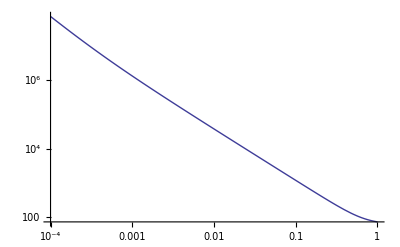

```mathematica
HL[10^-3]
HL1[10^-3]
LogLogPlot[HL[a],{a,10^-4,1}]
```

## f(R) Precise

```mathematica
Clear[Const1,Const2,Ω]
c=3*10^5;
h=0.71;
H0=100 h;
Ωx0 =0.73;
Ωm0 =0.27;
Ωr0 =8.09*10^-5;
fR0=0.02;
d1=6 Ωx0/Ωm0;
d2=-fR0 (12/Ωm0-9)^2
m=H0 √Ωm0;
lp=√(2.47*10^-25);
Const1=-(36(Ωx0/Ωm0)^2)/(12/Ωm0-9)^2 1/fR0;
Const2=-(6 Ωx0/Ωm0)/(12/Ωm0-9)^2 1/fR0;
Ω[a_]=Ωm0 a^-3+Ωr0 a^-4;
Ωm[a_]=Ωm0 a^-3;
Ωr[a_]=Ωr0 a^-4;
(*
ρcr= (3 H0^2)/κ^2;
ρm[a_]=ρcr Ωm0 a^-3;
ρr[a_]=ρcr Ωr0 a^-4;
ρ[a_]=ρm[a]+ρr[a];
pm[a_]=0;
pr[a_]=1/3 ρr[a];
p[a_]=pm[a]+pr[a];
*)
Hubb[a_]:=HubbleL[Ωr0,Ωm0,Ωx0,H0,a];
```

-25.1262

```mathematica
frp=3 (1-(Const1 mass^4)/((mass^2+12 Const2 H[a]^2+6 a Const2 H[a] H'[a])^2))==3 H0^2 (Ωm[a]+Ωr[a])+1/2 (-(Const1 mass^4 (12 H[a]^2+6 a H[a] H'[a]))/((mass^2+12 Const2 H[a]^2+6 a Const2 H[a] H'[a])^2)+(6 Const1 mass^2 H[a] (2 H[a]+a H'[a]))/(mass^2+12 Const2 H[a]^2+6 a Const2 H[a] H'[a]))-(6 a Const1 Const2 mass^4 H[a]^2 (30 H[a] H'[a]+6 a H'[a]^2+6 a H[a] H''[a]))/((mass^2+12 Const2 H[a]^2+6 a Const2 H[a] H'[a])^3)/.{mass->m}//Simplify
```

3+(5.82072×10^7)/((1361.07-7.74757 H[a]^2-3.87378 a H[a] H'[a])^2)==1/2 ((2.4469+8166.42 a)/a^4+(H[a] (2.32829×10^8 H[a]+1.16414×10^8 a H'[a]))/((1361.07-7.74757 H[a]^2-3.87378 a H[a] H'[a])^2)-(85531.5 H[a] (2 H[a]+a H'[a]))/(1361.07-7.74757 H[a]^2-3.87378 a H[a] H'[a])-(9.01928×10^8 a H[a]^2 (a H'[a]^2+H[a] (5. H'[a]+a H''[a])))/((1361.07-7.74757 H[a]^2-3.87378 a H[a] H'[a])^3))

```mathematica
HL[10^-2]
HL1[10^-2]
```

37441.4

-5.67065×10^6

```mathematica
hfrp=NDSolve[{frp,H[10^-2]==37,H'[10^-2]==-5},H[a],{a,10^-4,1}][[1]]
```

NDSolve::ndsz: At a == 0.01, step size is effectively zero; singularity or stiff system suspected.

{H[a]→InterpolatingFunction[{{0.01,1.}},<>][a]}

InterpolatingFunction::dmval: Input value {-4.60508} lies outside the range of data in the interpolating function. Extrapolation will be used.

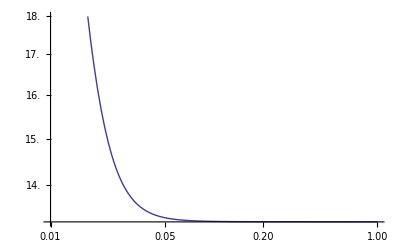

```mathematica
LogLogPlot[H[a]/.hfrp,{a,10^-2,1}]
```

## f(R) Gravity

f(R) signature

```mathematica
Clear[R,R1]
R[a_]=(-mass^2+2 Const1 mass^2+3 Const2 H0^2 Ω[a]-√(12 Const2 H0^2 mass^2 Ω[a]+(mass^2-2 Const1 mass^2-3 Const2 H0^2 Ω[a])^2))/(2 Const2)
R1[a_]=D[R[a],a]//Simplify
```

-0.774437 (-9763.87 (0.0000809/a^4+0.27/a^3)-21.9471 mass^2-√(-39055.5 (0.0000809/a^4+0.27/a^3) mass^2+(9763.87 (0.0000809/a^4+0.27/a^3)+21.9471 mass^2)^2))

-0.774437 (0.+(3.15959+7908.73 a)/a^5+(0.+4.9915/a^9+29153.1/a^8+(4.16987×10^7)/a^7+(126.049 mass^2)/a^5+(315513. mass^2)/a^4)/(2 √((0.623937+4164.72 a+6.94979×10^6 a^2+31.5123 a^4 mass^2+105171. a^5 mass^2+481.676 a^8 mass^4)/a^8)))

n is kinda special. Give the value of it first. Because when doing derivative

```mathematica
(*
Clear[f,fR]
(*fComp[Constant1_,Constant2_,mass_]=ffComp[4,Constant1,Constant2,mass]/.{R->R[a]};*)
f[Constant1_,Constant2_,mass_]=
fR[Constant1_,Constant2_,mass_]=ffR[1,Constant1,Constant2,mass]/.{R->R[a]}
fRR[Constant1_,Constant2_,mass_]=ffRR
*)
```

```mathematica
(*
Clear[f1,fR1,fR2]
f1[Constant1_,Constant2_,mass_]=Simplify[D[f[Constant1,Constant2,mass],a]]
fR1[Constant1_,Constant2_,mass_]=D[fR[Constant1,Constant2,mass],a]//Simplify
fR2[Constant1_,Constant2_,mass_]=D[D[fR[Constant1,Constant2,mass],a],a]
*)
```

Constants and fundamental functions. Units should be determined first.

```mathematica
Clear[Const1,Const2,Ω]
c=3*10^5;
h=0.71;
H0=100 h;
Ωx0 =0.73;
Ωm0 =0.27;
Ωr0 =8.09*10^-5;
fR0=0.02;
d1=6 Ωx0/Ωm0;
d2=-fR0 (12/Ωm0-9)^2
m=H0 √Ωm0;
lp=√(2.47*10^-25);
Const1=-(36(Ωx0/Ωm0)^2)/(12/Ωm0-9)^2 1/fR0;
Const2=-(6 Ωx0/Ωm0)/(12/Ωm0-9)^2 1/fR0;
Ω[a_]=Ωm0 a^-3+Ωr0 a^-4;
Ωm[a_]=Ωm0 a^-3;
Ωr[a_]=Ωr0 a^-4;
(*
ρcr= (3 H0^2)/κ^2;
ρm[a_]=ρcr Ωm0 a^-3;
ρr[a_]=ρcr Ωr0 a^-4;
ρ[a_]=ρm[a]+ρr[a];
pm[a_]=0;
pr[a_]=1/3 ρr[a];
p[a_]=pm[a]+pr[a];
*)
Hubb[a_]:=HubbleL[Ωr0,Ωm0,Ωx0,H0,a];
```

-25.1262

First equation: (Omega is the parameter for fraction evolution, so use )

```mathematica
f=-(Const1 mass^2 (-mass^2+2 Const1 mass^2+3 Const2 H0^2 Ω[a]-√(12 Const2 H0^2 mass^2 Ω[a]+((1-2 Const1) mass^2-3 Const2 H0^2 Ω[a])^2)))/(Const2 (mass^2+2 Const1 mass^2+3 Const2 H0^2 Ω[a]-√(12 Const2 H0^2 mass^2 Ω[a]+((1-2 Const1) mass^2-3 Const2 H0^2 Ω[a])^2)))/.{mass->m}
fR=-(4 Const1 mass^4)/((mass^2+2 Const1 mass^2+3 Const2 H0^2 Ω[a]-√(12 Const2 H0^2 mass^2 Ω[a]+((1-2 Const1) mass^2-3 Const2 H0^2 Ω[a])^2))^2)/.{mass->m}
fRR=-(16 Const1 Const2 mass^4)/((-mass^2-2 Const1 mass^2-3 Const2 H0^2 Ω[a]+√(12 Const2 H0^2 mass^2 Ω[a]+((1-2 Const1) mass^2-3 Const2 H0^2 Ω[a])^2))^3)/.{mass->m}
```

-(22079.6 (-29871.6-√((29871.6+9763.87 (0.0000809/a^4+0.27/a^3))^2-5.31572×10^7 (0.0000809/a^4+0.27/a^3))-9763.87 (0.0000809/a^4+0.27/a^3)))/(-27149.4-√((29871.6+9763.87 (0.0000809/a^4+0.27/a^3))^2-5.31572×10^7 (0.0000809/a^4+0.27/a^3))-9763.87 (0.0000809/a^4+0.27/a^3))

(7.76096×10^7)/((-27149.4-√((29871.6+9763.87 (0.0000809/a^4+0.27/a^3))^2-5.31572×10^7 (0.0000809/a^4+0.27/a^3))-9763.87 (0.0000809/a^4+0.27/a^3))^2)

-(2.00428×10^8)/((27149.4+√((29871.6+9763.87 (0.0000809/a^4+0.27/a^3))^2-5.31572×10^7 (0.0000809/a^4+0.27/a^3))+9763.87 (0.0000809/a^4+0.27/a^3))^3)

Friedmann Equation in f(R) theory

```mathematica
fried=3 (1-(4 Const1 mass^4)/(mass^2+2 Const1 mass^2+3 Const2 H0^2 Ω[a]+√(12 Const2 H0^2 mass^2 Ω[a]+((1-2 Const1) mass^2-3 Const2 H0^2 Ω[a])^2))^2)==1/2 ((Const1 mass^2 (-mass^2+2 Const1 mass^2+3 Const2 H0^2 Ω[a]+√(12 Const2 H0^2 mass^2 Ω[a]+((1-2 Const1) mass^2-3 Const2 H0^2 Ω[a])^2)))/(Const2 (mass^2+2 Const1 mass^2+3 Const2 H0^2 Ω[a]+√(12 Const2 H0^2 mass^2 Ω[a]+((1-2 Const1) mass^2-3 Const2 H0^2 Ω[a])^2)))+1/(2 Const2)(-mass^2+2 Const1 mass^2+3 Const2 H0^2 Ω[a]+√(12 Const2 H0^2 mass^2 Ω[a]+(mass^2-2 Const1 mass^2-3 Const2 H0^2 Ω[a])^2)) (1+(4 Const1 mass^4)/(mass^2+2 Const1 mass^2+3 Const2 H0^2 Ω[a]+√(12 Const2 H0^2 mass^2 Ω[a]+((1-2 Const1) mass^2-3 Const2 H0^2 Ω[a])^2))^2))+3 H0^2 (Ωm[a]+Ωr[a])-(24 a Const1 mass^4 H[a]^2 (3 Const2 H0^2 Ω'[a]+(12 Const2 H0^2 mass^2 Ω'[a]-6 Const2 H0^2 (mass^2-2 Const1 mass^2-3 Const2 H0^2 Ω[a]) Ω'[a])/(2 √(12 Const2 H0^2 mass^2 Ω[a]+(mass^2-2 Const1 mass^2-3 Const2 H0^2 Ω[a])^2))))/((mass^2+2 Const1 mass^2+3 Const2 H0^2 Ω[a]+√(12 Const2 H0^2 mass^2 Ω[a]+((1-2 Const1) mass^2-3 Const2 H0^2 Ω[a])^2))^3)/.{mass->m};
```

## Background Comparison with LCDM model.

Here is a comparison of different calculations. H is the only R approx. method; Hb is the benchmark; Htt is the method used before; HL is the LCDM standard.

Stiff functions present. Needs stiff solving.

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["FunctionApproximations`"];
```

Try to solve the exact function of Hubble function.

```mathematica
H[a]√(1-(Const1 mass^4)/((mass^2+Const2 (12 H[a]^2+6 a H[a] H'[a]))^2)+(2 a Const1 Const2 mass^4 (30 H[a] H'[a]+6 a H'[a]^2+6 a H[a] H''[a]))/((mass^2+Const2 (12 H[a]^2+6 a H[a] H'[a]))^3))==(√(H0^2 Ωm[a]+H0^2 Ωr[a]-(Const1 mass^4 (12 H[a]^2+6 a H[a] H'[a]))/(6 (mass^2+Const2 (12 H[a]^2+6 a H[a] H'[a]))^2)+(Const1 (12 H[a]^2+6 a H[a] H'[a]))/(6 (1+(Const2 (12 H[a]^2+6 a H[a] H'[a]))/mass^2))))/(√(1-(Const1 mass^4)/((mass^2+Const2 (12 H[a]^2+6 a H[a] H'[a]))^2)+(2 a Const1 Const2 mass^4 (30 H[a] H'[a]+6 a H'[a]^2+6 a H[a] H''[a]))/((mass^2+Const2 (12 H[a]^2+6 a H[a] H'[a]))^3)))/.{mass-> m}


hubfuncpre=(H[a]√(1-(Const1 mass^4)/((mass^2+Const2 (12 H[a]^2+6 a H[a] H'[a]))^2)+(2 a Const1 Const2 mass^4 (30 H[a] H'[a]+6 a H'[a]^2+6 a H[a] H''[a]))/((mass^2+Const2 (12 H[a]^2+6 a H[a] H'[a]))^3)))^2==((√(H0^2 Ωm[a]+H0^2 Ωr[a]-(Const1 mass^4 (12 H[a]^2+6 a H[a] H'[a]))/(6 (mass^2+Const2 (12 H[a]^2+6 a H[a] H'[a]))^2)+(Const1 (12 H[a]^2+6 a H[a] H'[a]))/(6 (1+(Const2 (12 H[a]^2+6 a H[a] H'[a]))/mass^2))))/(√(1-(Const1 mass^4)/((mass^2+Const2 (12 H[a]^2+6 a H[a] H'[a]))^2)+(2 a Const1 Const2 mass^4 (30 H[a] H'[a]+6 a H'[a]^2+6 a H[a] H''[a]))/((mass^2+Const2 (12 H[a]^2+6 a H[a] H'[a]))^3))))^2/.{mass-> m}//Simplify
HL[10^-4]
HL1[10^-4]
```

H[a] √(1+(1.94024×10^7)/((1361.07-0.64563 (12 H[a]^2+6 a H[a] H'[a]))^2)+(2.50535×10^7 a (30 H[a] H'[a]+6 a H'[a]^2+6 a H[a] H''[a]))/((1361.07-0.64563 (12 H[a]^2+6 a H[a] H'[a]))^3))==(√(0.407817/a^4+1361.07/a^3+(3.23373×10^6 (12 H[a]^2+6 a H[a] H'[a]))/((1361.07-0.64563 (12 H[a]^2+6 a H[a] H'[a]))^2)-(1.74559 (12 H[a]^2+6 a H[a] H'[a]))/(1-0.000474355 (12 H[a]^2+6 a H[a] H'[a]))))/(√(1+(1.94024×10^7)/((1361.07-0.64563 (12 H[a]^2+6 a H[a] H'[a]))^2)+(2.50535×10^7 a (30 H[a] H'[a]+6 a H'[a]^2+6 a H[a] H''[a]))/((1361.07-0.64563 (12 H[a]^2+6 a H[a] H'[a]))^3)))

H[a]^2 (1+(1.94024×10^7)/((1361.07-7.74757 H[a]^2-3.87378 a H[a] H'[a])^2)+(1.50321×10^8 a (a H'[a]^2+H[a] (5. H'[a]+a H''[a])))/((1361.07-7.74757 H[a]^2-3.87378 a H[a] H'[a])^3))==(0.407817/a^4+1361.07/a^3+(H[a] (3.88048×10^7 H[a]+1.94024×10^7 a H'[a]))/((1361.07-7.74757 H[a]^2-3.87378 a H[a] H'[a])^2)+(H[a] (-20.9471 H[a]-10.4736 a H'[a]))/(1.-0.00569226 H[a]^2-0.00284613 a H[a] H'[a]))/(1+(1.94024×10^7)/((1361.07-7.74757 H[a]^2-3.87378 a H[a] H'[a])^2)+(1.50321×10^8 a (a H'[a]^2+H[a] (5. H'[a]+a H''[a])))/((1361.07-7.74757 H[a]^2-3.87378 a H[a] H'[a])^3))

7.37512×10^7

-1.38275×10^12

```mathematica
NDSolve[{hubfuncpre,H[10^-2]==HL[10^-2],H'[10^-2]==HL1[10^-2]},H[a],{a,10^-4,1},Method->{StiffnessSwitching,Method->{ExplicitRungeKutta,Automatic}}]
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point a == 0.00999956.

General::ovfl: Overflow occurred in computation.

NDSolve::nlnum: The function value {2.46136011258857×10^33763439, Overflow[]} is not a list of numbers with dimensions {2} at aH[a]SuperscriptBox[ = {0.0142219, 2.60855105597718×10^9479977, 2.46136011258857×10^33763439}.

NDSolve::ndsz: At a == 0.01, step size is effectively zero; singularity or stiff system suspected.

{{H[a]→InterpolatingFunction[{{0.00999956,0.01}},<>][a]},{H[a]→InterpolatingFunction[{{0.01,0.01}},<>][a]}}

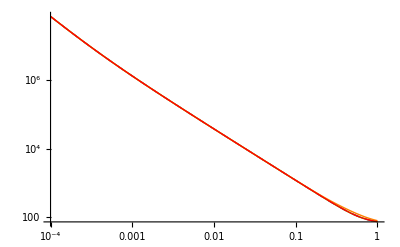

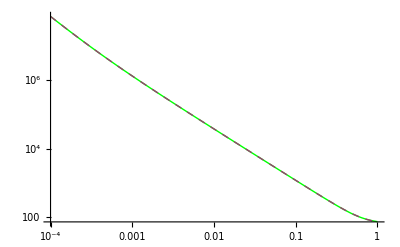

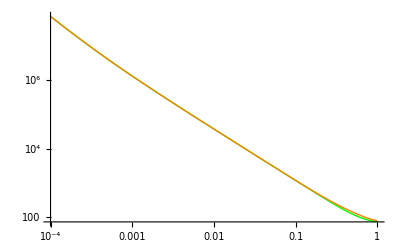

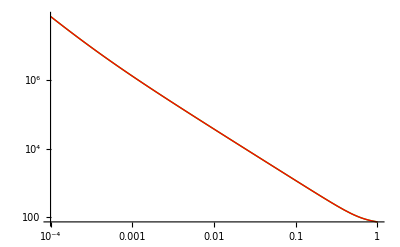

```mathematica
LogLogPlot[{H[a],HL[a],Htt[a],Hb[a]},{a,10^-4,1},PlotStyle->{Green,Dashed,Orange,Red},PlotLegend->{"H","HL","Htt","Hb"}]
LogLogPlot[{H[a],HL[a]},{a,10^-4,1},PlotStyle->{Green,Dashed},PlotLegend->{"H","HL"}]
LogLogPlot[{H[a],Htt[a]},{a,10^-4,1},PlotStyle->{Green,Orange},PlotLegend->{"H","Htt"}]
LogLogPlot[{H[a],Hb[a]},{a,10^-4,1},PlotStyle->{Green,Red},PlotLegend->{"H","Hb"}]
```

```mathematica
H1[aa]/H[aa]//Simplify;
```

H1[a] is the first derivative of H[a]

```mathematica
wleff[a_]=-1-2/3 a HL1[a]/HL[a];
wmeff[a_]=-1-2/3 a HM1[a]/HM[a];
weff[a_]=-1-2/3 a H1[a]/H[a];
wtteff[a_]=-1-2/3 a Htt1[a]/Htt[a];
wdeff[a_]=-1-1/3((a(2H[a] H1[a])/m^2+3 a^-3)/(H[a]^2/m^2-a^-3));
wldeff[a_]=-1-1/3((a(2HL[a] HL1[a])/m^2+3 a^-3)/(HL[a]^2/m^2-a^-3));
wttdeff[a_]=-1-1/3((a(2Htt[a] Htt1[a])/m^2+3 a^-3)/(Htt[a]^2/m^2-a^-3));
```

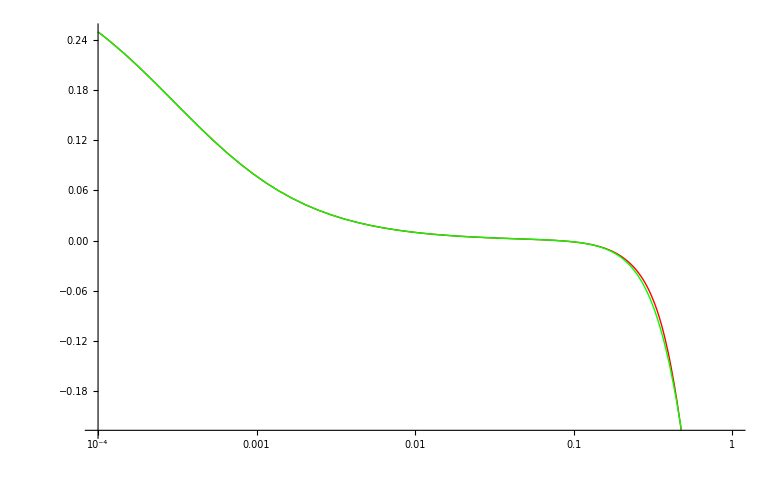

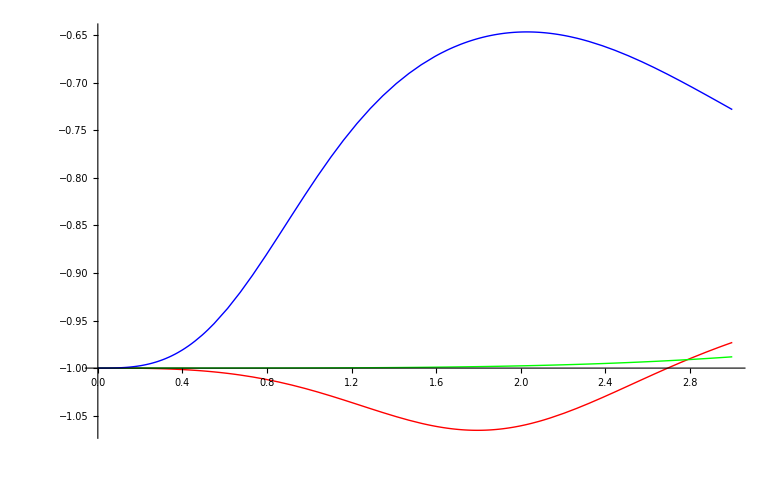

```mathematica
LogLinearPlot[{weff[a],wleff[a]},{a,0.0001,1},PlotStyle->{Red,Green,Blue}]
Plot[{wdeff[1/mn],wldeff[1/mn],wttdeff[1/mn]},{mn,0.001,3},PlotStyle->{Red,Green,Blue}]
```

```mathematica
weff[0.3]
H1[0.1]
HL1[0.3]
HL[0.3]
H[0.3]
```

-0.0606335

-17520.2

-1084.69

232.681

232.04

## f(R) Gravity Perturbation

LCDM Model data

138

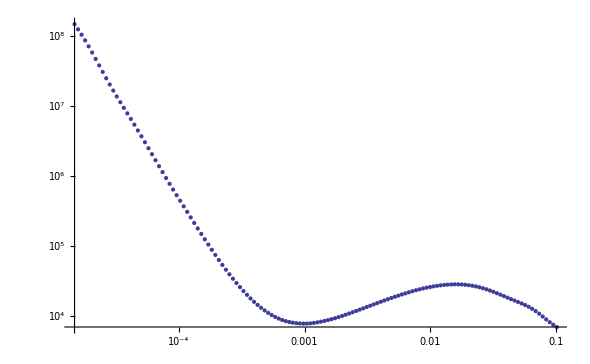

NIntegrate::nlim: temp = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

```mathematica
Clear[GrowthL]
PowerL=Import["cdm_invariant_cut.dat"];
lent=Length[PowerL]
ListLogLogPlot[PowerL]
GrowthL[a_]:= 5/2 Ωm0  HL[a,H0,Ωm0,Ωr0,Ωx0]/H0 NIntegrate[1/(iHL[temp]/H0)^3,{temp,0,a}];
GrowthL1[a_]=D[GrowthL[a],a];
```

Check the divation from LCDM : M

```mathematica
Clear[k,a,dH,dHL,temp,chih2]
dH[a_?NumberQ]:= c a NIntegrate[1/(temp^2 H[temp]),{temp,0,a},MinRecursion->4]
dHL[a_?NumberQ]:=c a NIntegrate[1/(temp^2 HL[temp]),{temp,0,a}]
k[a_]:=1/dH[a]
kL[a_]:=1/dHL[a]
```

0.980256

0.980256

0.980255

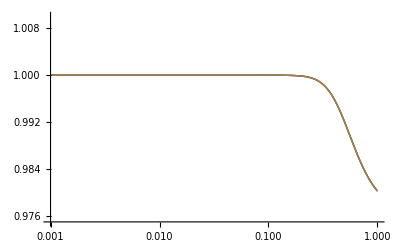

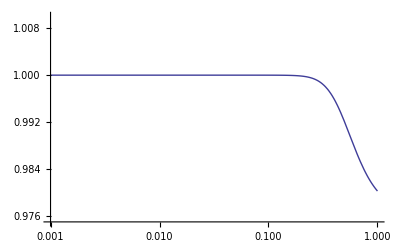
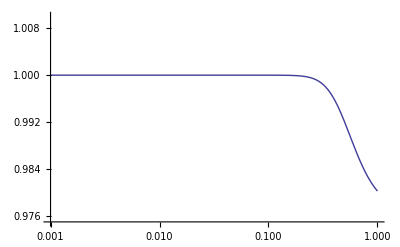
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
chih2[a_,kk_]=1/(fR+1)(4fRR+(fR+1-R[a] fRR)a^2/kk^2)/(3fRR+(fR+1-R[a] fRR)a^2/kk^2)/.{mass->m}//Simplify;
chih2[1,0.01]
chih2[1,0.1]
chih2[1,0.5]
LogLinearPlot[{chih2[a,0.001],chih2[a,0.01],chih2[a,0.1]},{a,0.001,1},PlotRange->{0.975,1.01}]
Table[{LogLinearPlot[chih2[a,0.001],{a,0.001,1},PlotRange->{0.975,1.01}],LogLinearPlot[chih2[a,0.01],{a,0.001,1},PlotRange->{0.975,1.01}],LogLinearPlot[chih2[a,0.1],{a,0.001,1},PlotRange->{0.975,1.01}]}]
```

```mathematica
Manipulate[LogLinearPlot[chih2[a,kk],{a,10^-4,1},PlotRange->{0.975,1.01}],{kk,0.001,0.1}]
```

```mathematica
(*
xx[a_]=Block[{kk,gg},kk=h PowerL[[100,1]];NDSolve[{a^2*gg''[a]+a^2*(H1[a]/H[a]+3/a)gg'[a]-3/2 chih2[a,kk] H0^2 Ωm0 a^-3/H[a]^2 gg[a]==0,gg[10^-3]==GrowthL[10^-3],gg'[10^-3]==GrowthL'[10^-3]},gg[a],{a,0.001,10}][[1]][[1]]]
xx[10]
xxx[a_]=Block[{kk=h PowerL[[nn,1]]},NDSolve[{a^2×∂_(a,a) DgL[a]+3/2×a×(1+H[a]^-2×H0^2×Ωx0)×∂_a DgL[a]-3/2×chih2[a,kk]*H[a]^-2×H0^2×Ωm0 a^-3×DgL[a]==0,DgL[10^-3]==N[GrowthL[10^-3]],DgL'[10^-2]==N[GrowthL'[10^-2]]},DgL[a],{a,0.001,1}][[1]][[1]]];
xxxx[a_]=Block[{kk=h PowerL[[1,1]]},NDSolve[{∂_(a,a) DgL[a]+(3/a+HL1[a]/HL[a])×∂_a DgL[a]-3/2 1/(a^2 HL[a]^2)H0^2×(Ωm0 a^-3+Ωx0)×DgL[a]==0,DgL[10^-3]==N[GrowthL[10^-3]],DgL'[10^-2]==N[GrowthL'[10^-2]]},DgL[a],{a,0.001,1}][[1]][[1]]];
*)
```

```mathematica
xx[0.1]
GrowthL[0.01]
```

xx[0.1]

0.0101487

```mathematica
PowerL[[nn,1]]==k[an];
```

Part::pspec: Part specification nn is neither an integer nor a list of integers.

```mathematica
solgf=NDSolve[{a^2*gg''[a]+a^2*(H1[a]/H[a]+3/a-Ωx0/H[a]^2)gg'[a]-3/2 H0^2 Ωm0 a^-3/H[a]^2 gg[a]==0,gg[10^-3]==GrowthL[10^-3],gg'[10^-4]==GrowthL'[10^-4]},gg[a],{a,0.001,1}][[1]]
Growth[a_]=gg[a]/.solgf[[1]]
```

NIntegrate::nlim: temp = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{gg[a]→InterpolatingFunction[{{0.001,1.}},<>][a]}

InterpolatingFunction[{{0.001,1.}},<>][a]

```mathematica
solgft=NDSolve[{a^2*ggt''[a]+a^2*(H1[a]/H[a]+3/a)ggt'[a]-3/2 H0^2 Ωm0 a^-3/H[a]^2 ggt[a]==0,ggt[10^-3]==GrowthL[10^-3],ggt'[10^-3]==GrowthL'[10^-3]},ggt[a],{a,0.001,1}][[1]]
Growtht[a_]=ggt[a]/.solgft[[1]]
```

NIntegrate::nlim: temp = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{ggt[a]→InterpolatingFunction[{{0.001,1.}},<>][a]}

InterpolatingFunction[{{0.001,1.}},<>][a]

NIntegrate::nlim: temp = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

InterpolatingFunction[{{0.001,1.}},<>][a]

InterpolatingFunction::dmval: Input value {-9.21015} lies outside the range of data in the interpolating function. Extrapolation will be used.

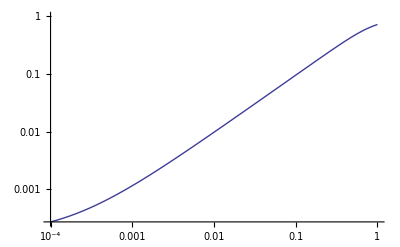

```mathematica
Clear[Growthb]
Growthb[a_]=ggb[a]/.NDSolve[{a^2*ggb''[a]+a^2*(H1[a]/H[a]+3/a-Ωx0/H[a]^2)ggb'[a]-3/2 chih2[a,0.1] H0^2 Ωm0 a^-3/H[a]^2 ggb[a]==0,ggb[10^-3]==GrowthL[10^-3],ggb'[10^-4]==GrowthL'[10^-4]},ggb[a],{a,0.001,1}][[1]][[1]]
LogLogPlot[Growthb[a],{a,0.0001,1}]
```

```mathematica
solgfb:=NDSolve[{a^2*ggb''[a]+a^2*(H1[a]/H[a]+3/a-Ωx0/H[a]^2)ggb'[a]-3/2 chih2[a,kk] H0^2 Ωm0 a^-3/H[a]^2 ggb[a]==0,ggb[10^-3]==GrowthL[10^-3],ggb'[10^-4]==GrowthL'[10^-4]},ggb[a],{a,0.001,1}][[1]]
Growthb[a_]:=ggb[a]/.solgfb[[1]]
Manipulate[LogLogPlot[Growthb[a],{a,0.0001,1}],{kk,0.01,0.1}];
Manipulate[Quiet[Growthb[a_]=ggb[a]/.NDSolve[{a^2*ggb''[a]+a^2*(H1[a]/H[a]+3/a-Ωx0/H[a]^2)ggb'[a]-3/2 chih2[a,kk] H0^2 Ωm0 a^-3/H[a]^2 ggb[a]==0,ggb[10^-3]==GrowthL[10^-3],ggb'[10^-4]==GrowthL'[10^-4]},ggb[a],{a,0.001,1}][[1]][[1]]];Quiet[LogLogPlot[Growthb[a],{a,0.0001,1}]],{kk,0.001,0.1}]
```

InterpolatingFunction::dmval: Input value {-9.21015} lies outside the range of data in the interpolating function. Extrapolation will be used.

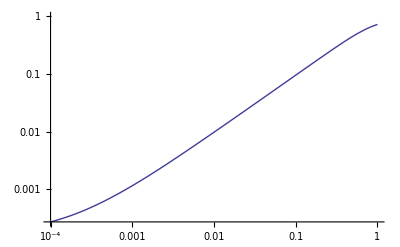

```mathematica
LogLogPlot[Growth[a],{a,0.0001,1}]
```

```mathematica
solgl=NDSolve[{a^2*ggl''[a]+a^2*(HL1[a]/HL[a]+3/a)ggl'[a]-3/2  H0^2 Ωm0 a^-3/HL[a]^2 ggl[a]==0,ggl[10^-3]==GrowthL[10^-3],ggl'[10^-3]==GrowthL'[10^-3]},ggl,{a,0.001,1}][[1]]
Growthl[a_]:=ggl[a]/.solgl[[1]]
```

NIntegrate::nlim: temp = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{ggl→InterpolatingFunction[{{0.001,1.}},<>]}

InterpolatingFunction::dmval: Input value {-9.21015} lies outside the range of data in the interpolating function. Extrapolation will be used.

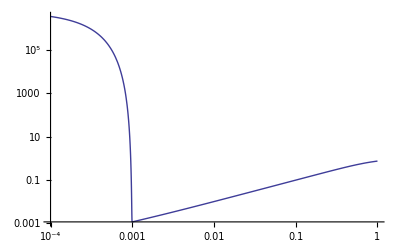

```mathematica
LogLogPlot[Growthl[a],{a,0.0001,1}]
```

The growth factor of f(R) becomes very large in the future. This is because this calculation doesn’t hold for late time for a approximation of R has been used.

NIntegrate::nlim: temp = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.217156} lies outside the range of data in the interpolating function. Extrapolation will be used.

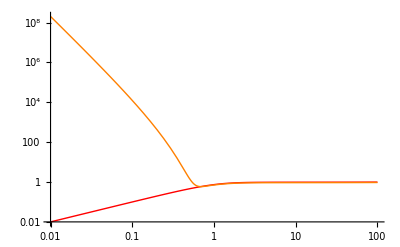

InterpolatingFunction::dmval: Input value {-0.217158} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

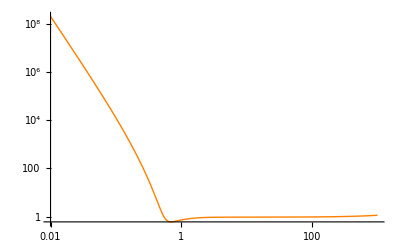
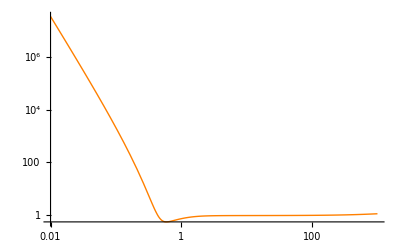
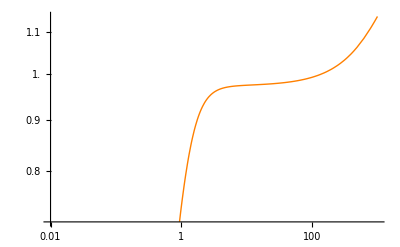

```mathematica
LogLogPlot[{mn GrowthL[1/mn],mn Growth[1/mn]},{mn,0.01,100},PlotStyle->{Red,Orange},PlotLegend->{"LCDM_L", "f(R)"},LegendPosition->{1.1,-0.4}]
Table[{LogLogPlot[mn Growth[1/mn],{mn,0.01,1000},PlotStyle->Orange,PlotLegend->"f(R)",LegendPosition->{1.1,-0.4}],LogLogPlot[mn Growtht[1/mn],{mn,0.01,1000},PlotStyle->Orange,PlotLegend->"f(R)",LegendPosition->{1.1,-0.4}],LogLogPlot[mn Growthl[1/mn],{mn,0.01,1000},PlotStyle->Orange,PlotLegend->"LCDM Test",LegendPosition->{1.1,-0.4}]}]
```

```mathematica
ain=Table[ai/.FindRoot[PowerL[[i,1]]h==k[ai],{ai,0.0001}],{i,1,lent}]
aL=Table[aL/.FindRoot[PowerL[[i,1]]h==kL[aL],{aL,0.0001}],{i,1,lent}]
```

{5.31719,5.0005,4.70361,4.42527,4.16434,3.91971,3.69037,3.47537,3.2738,3.08482,2.90764,2.74152,2.58577,2.43974,2.30281,2.17441,2.05401,1.94109,1.83519,1.73585,1.64265,1.55522,1.47316,1.39615,1.32384,1.25594,1.19215,1.1322,1.07584,1.02283,0.972934,0.925953,0.881684,0.839944,0.800559,0.763368,0.728221,0.694978,0.66351,0.633697,0.605428,0.578601,0.553122,0.528904,0.505866,0.483937,0.463048,0.443138,0.42415,0.406032,0.388736,0.372218,0.356437,0.341355,0.326937,0.31315,0.299963,0.287349,0.275278,0.263728,0.252673,0.242091,0.231961,0.222262,0.212976,0.204083,0.195567,0.187412,0.179601,0.172119,0.164953,0.158089,0.151514,0.145215,0.13918,0.133399,0.127861,0.122554,0.11747,0.112599,0.107932,0.10346,0.0991755,0.0950699,0.0911359,0.0873664,0.0837542,0.0802929,0.0769761,0.0737977,0.0707519,0.0678332,0.0650361,0.0623556,0.0597868,0.057325,0.0549658,0.0527047,0.0505378,0.048461,0.0464707,0.044563,0.0427347,0.0409824,0.0393029,0.0376931,0.0361502,0.0346713,0.0332538,0.0318951,0.0305927,0.0293443,0.0281476,0.0270005,0.0259009,0.0248468,0.0238363,0.0228677,0.021939,0.0210487,0.0201953,0.019377,0.0185925,0.0178404,0.0171193,0.0164279,0.015765,0.0151294,0.01452,0.0139356,0.0133753,0.012838,0.0123227,0.0118287,0.0113548,0.0109004,0.0104647,0.0100468}

{5.28897,4.97449,4.67966,4.40327,4.14415,3.90122,3.67348,3.45997,3.25979,3.07212,2.89616,2.73119,2.57651,2.43147,2.29547,2.16794,2.04834,1.93617,1.83096,1.73226,1.63966,1.55276,1.4712,1.39463,1.32273,1.25519,1.19172,1.13206,1.07594,1.02313,0.973413,0.926571,0.88241,0.840749,0.801416,0.764254,0.729113,0.695859,0.664364,0.634511,0.606192,0.579308,0.553767,0.529484,0.506383,0.484391,0.463442,0.443476,0.424438,0.406274,0.388937,0.372384,0.356573,0.341465,0.327025,0.31322,0.300019,0.287392,0.275313,0.263754,0.252693,0.242107,0.231973,0.222271,0.212983,0.204088,0.195571,0.187415,0.179603,0.172121,0.164955,0.15809,0.151514,0.145215,0.139181,0.133399,0.127861,0.122554,0.11747,0.112599,0.107932,0.10346,0.0991755,0.0950699,0.091136,0.0873664,0.0837542,0.0802929,0.0769761,0.0737977,0.0707519,0.0678332,0.0650361,0.0623556,0.0597868,0.057325,0.0549658,0.0527047,0.0505378,0.048461,0.0464707,0.044563,0.0427347,0.0409824,0.0393029,0.0376931,0.0361502,0.0346713,0.0332538,0.0318951,0.0305927,0.0293443,0.0281476,0.0270005,0.0259009,0.0248468,0.0238363,0.0228677,0.021939,0.0210487,0.0201953,0.019377,0.0185925,0.0178404,0.0171193,0.0164279,0.015765,0.0151294,0.01452,0.0139356,0.0133753,0.012838,0.0123227,0.0118287,0.0113548,0.0109004,0.0104647,0.0100468}

```mathematica
Export["ModifiedGravity\\fRGravity\\Data\\ain.xls",ain,"XLS"]
Export["ModifiedGravity\\fRGravity\\Data\\aL.xls",aL,"XLS"]
```

ModifiedGravity\fRGravity\Data\ain.xls

ModifiedGravity\fRGravity\Data\aL.xls

Find the transition points & fractions

```mathematica
trans=29;transL=28;
frac:=1/((Growth[1]/Growth[ain[[lent]]])/(GrowthL[1]/GrowthL[aL[[lent]]]));
```

Q factors

```mathematica
qFactor=Table[{PowerL[[i+trans,1]],frac(Growth[1]/Growth[ain[[i+trans]]])/(GrowthL[1]/GrowthL[aL[[i+trans]]])},{i,1,lent-trans}];
qFactorEx=Table[{PowerL[[i,1]],frac(Growth[1]/Growth[ain[[trans]]])/(GrowthL[1]/GrowthL[aL[[trans]]])},{i,1,trans}];
```

InterpolatingFunction::dmval: Input value {1.02283} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.07584} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

```mathematica
qFactor;
```

```mathematica
qFactorEx;
```

```mathematica
qFac=Join[qFactorEx,qFactor];
```

```mathematica
power=Table[{PowerL[[i,1]],(qFac[[i]][[2]])^2 PowerL[[i,2]]},{i,1,lent}];
Export["ModifiedGravity\\fRGravity\\Data\\Power.xls",power,"XLS"]
```

ModifiedGravity\fRGravity\Data\Power.xls

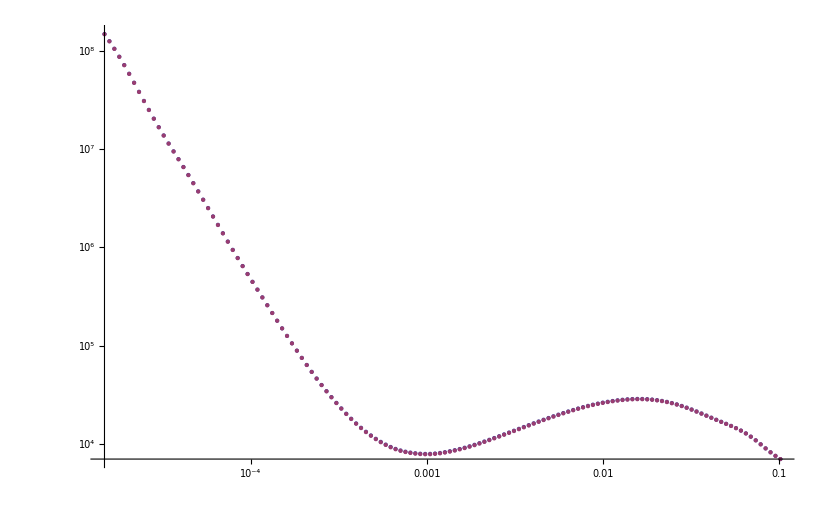

```mathematica
ListLogLogPlot[{power,PowerL}]
```

{{0.0000147064,0.00234337},{0.0000156873,0.00234337},{0.0000167336,0.00234337},{0.0000178496,0.00234337},{0.0000190402,0.00234337},{0.0000203101,0.00234337},{0.0000216647,0.00234337},{0.0000231097,0.00234337},{0.000024651,0.00234337},{0.0000262952,0.00234337},{0.000028049,0.00234337},{0.0000299197,0.00234337},{0.0000319153,0.00234337},{0.0000340439,0.00234337},{0.0000363146,0.00234337},{0.0000387366,0.00234337},{0.0000413202,0.00234337},{0.0000440762,0.00234337},{0.0000470159,0.00234337},{0.0000501517,0.00234337},{0.0000534967,0.00234337},{0.0000570647,0.00234337},{0.0000608708,0.00234337},{0.0000649306,0.00234337},{0.0000692613,0.00234337},{0.0000738808,0.00234337},{0.0000788084,0.00234337},{0.0000840647,0.00234337},{0.0000896716,0.00234337},{0.0000956524,0.0020152},{0.000102032,0.00170807},{0.000108837,0.00143871},{0.000116096,0.00121185},{0.00012384,0.00103133},{0.000132099,0.000899999},{0.00014091,0.000819524},{0.000150308,0.000790284},{0.000160333,0.000811309},{0.000171027,0.000880276},{0.000182434,0.000993577},{0.000194602,0.00114645},{0.000207581,0.00133319},{0.000221426,0.00154734},{0.000236194,0.00178205},{0.000251948,0.00203032},{0.000268752,0.00228531},{0.000286677,0.00254062},{0.000305797,0.00279055},{0.000326193,0.00303024},{0.000347949,0.00325583},{0.000371156,0.00346445},{0.000395911,0.00365424},{0.000422317,0.00382426},{0.000450484,0.00397435},{0.00048053,0.00410501},{0.00051258,0.00421725},{0.000546768,0.0043124},{0.000583235,0.00439203},{0.000622135,0.00445778},{0.00066363,0.00451131},{0.000707892,0.0045542},{0.000755106,0.00458794},{0.000805469,0.00461387},{0.000859191,0.00463316},{0.000916496,0.00464686},{0.000977624,0.00465584},{0.00104283,0.00466085},{0.00111238,0.00466253},{0.00118657,0.00466137},{0.00126571,0.00465782},{0.00135013,0.00465219},{0.00144018,0.00464476},{0.00153624,0.00463576},{0.0016387,0.00462534},{0.001748,0.00461365},{0.00186458,0.00460077},{0.00198895,0.0045868},{0.0021216,0.00457176},{0.00226311,0.00455571},{0.00241405,0.00453865},{0.00257506,0.00452061},{0.00274681,0.00450158},{0.00293001,0.00448155},{0.00312543,0.00446052},{0.00333389,0.00443845},{0.00355625,0.00441532},{0.00379344,0.00439111},{0.00404645,0.00436578},{0.00431633,0.0043393},{0.00460422,0.00431162},{0.0049113,0.00428271},{0.00523887,0.00425251},{0.00558829,0.00422098},{0.00596101,0.00418807},{0.00635859,0.00415373},{0.00678269,0.0041179},{0.00723507,0.00408051},{0.00771763,0.00404151},{0.00823237,0.00400084},{0.00878144,0.00395842},{0.00936714,0.00391419},{0.0099919,0.00386807},{0.0106583,0.00381999},{0.0113692,0.00376986},{0.0121275,0.0037176},{0.0129364,0.00366313},{0.0137992,0.00360636},{0.0147195,0.00354719},{0.0157013,0.00348553},{0.0167485,0.00342126},{0.0178656,0.0033543},{0.0190571,0.00328453},{0.0203282,0.00321183},{0.021684,0.00313608},{0.0231303,0.00305717},{0.024673,0.00297497},{0.0263186,0.00288933},{0.028074,0.00280013},{0.0299464,0.00270722},{0.0319438,0.00261044},{0.0340743,0.00250966},{0.0363469,0.0024047},{0.0387712,0.00229539},{0.0413571,0.00218158},{0.0441155,0.00206306},{0.0470578,0.00193967},{0.0501964,0.0018112},{0.0535444,0.00167745},{0.0571156,0.00153822},{0.0609251,0.00139329},{0.0649886,0.00124244},{0.0693231,0.00108543},{0.0739467,0.000922019},{0.0788787,0.000751967},{0.0841397,0.000575012},{0.0897515,0.000390885},{0.0957377,0.00019931},{0.102123,-1.11022×10^-16}}

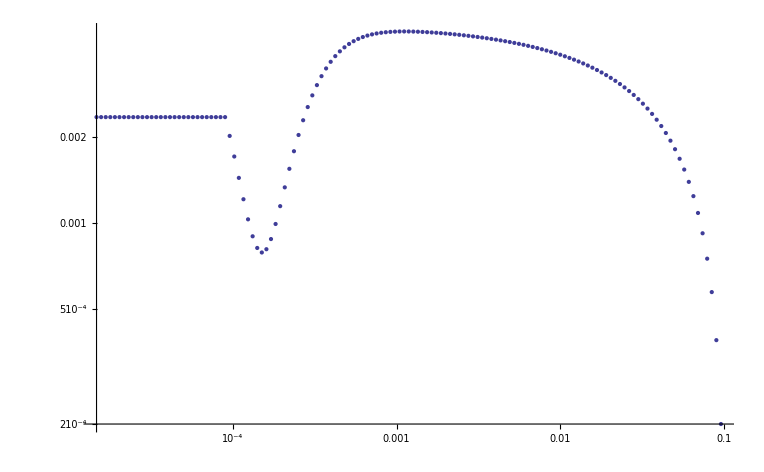

```mathematica
deltaqFac=Table[{qFac[[i,1]],qFac[[i,2]]-1},{i,1,lent}]
ListLogLogPlot[deltaqFac]
```

## Backup here

```mathematica
Clear[H]
fRFriedmann=3(1+fR)==3 H0^2/c^2(Ωm0 a^-3+Ωr0 a^-4)+((1-fR)R-f)/2-3a H[a]^2 fRR R1//FullSimplify
```

$Aborted

```mathematica
Solve[ H[a]^2==(3 c^2)/(3a fRR R1) H0^2/c^2(Ωm0 a^-3+Ωr0 a^-4)+((1-fR)R-f)/2-3(1+fR),H[a]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H[a]→-1.67634×10^-52 √(7.85609×10^107-(1.50539×10^119)/((44159.2+4083.21/a^3)^3)-(3.48314×10^115)/((44159.2+4083.21/a^3)^2)+(9.20216×10^99)/(44159.2+4083.21/a^3)+(8.87661×10^104)/(0.0003236+0.81 a)+(7.01762×10^101)/((0.0003236+0.81 a) a^9)+(2.3421×10^105)/((0.0003236+0.81 a) a^8)+(2.27683×10^103)/((0.0003236+0.81 a) a^6)+(7.59881×10^106)/((0.0003236+0.81 a) a^5)+(7.26518×10^106)/a^3-(1.42581×10^118)/((44159.2+4083.21/a^3)^3 a^3)-(3.38169×10^114)/((44159.2+4083.21/a^3)^2 a^3)+(2.46235×10^104)/((0.0003236+0.81 a) a^3)+(8.21797×10^107)/((0.0003236+0.81 a) a^2)+(2.96253×10^108 a)/(0.0003236+0.81 a))},{H[a]→1.67634×10^-52 √(7.85609×10^107-(1.50539×10^119)/((44159.2+4083.21/a^3)^3)-(3.48314×10^115)/((44159.2+4083.21/a^3)^2)+(9.20216×10^99)/(44159.2+4083.21/a^3)+(8.87661×10^104)/(0.0003236+0.81 a)+(7.01762×10^101)/((0.0003236+0.81 a) a^9)+(2.3421×10^105)/((0.0003236+0.81 a) a^8)+(2.27683×10^103)/((0.0003236+0.81 a) a^6)+(7.59881×10^106)/((0.0003236+0.81 a) a^5)+(7.26518×10^106)/a^3-(1.42581×10^118)/((44159.2+4083.21/a^3)^3 a^3)-(3.38169×10^114)/((44159.2+4083.21/a^3)^2 a^3)+(2.46235×10^104)/((0.0003236+0.81 a) a^3)+(8.21797×10^107)/((0.0003236+0.81 a) a^2)+(2.96253×10^108 a)/(0.0003236+0.81 a))}}

```mathematica
Clear[Sol]
Sol[a_]=NDSolve[{fRFriedmann,H[10^-3]==HL[10^-3,H0,Ωm0,Ωr0,Ωx0],H'[10^-3]==HL1[10^-3,H0,Ωm0,Ωr0,Ωx0]},H[a],{a,10^-4,1}]
```

NDSolve::ivcon: The given initial conditions were not consistent with the differential-algebraic equations. NDSolve will attempt to correct the values.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

{}

Testing Functions

```mathematica
t1=Table[i*10^-4,{i,1,10,0.1}];
t2=Table[i*10^-3,{i,1,10,0.1}];
t3=Table[i*10^-2,{i,1,10,0.1}];
t4=Table[i*10^-1,{i,1,10,0.1}];
t5=Table[i,{i,1,1,0.1}];
aTable=Join[t1,t2,t3,t4,t5];
Length[aTable]
ListPlot[aTable];
```

365

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

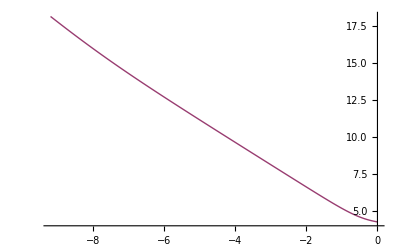

```mathematica
HubbleTable=Table[{Sol[aTable[[i]]][[1]][[1]],HL[aTable[[i]],H0,Ωm0,Ωr0,Ωx0],aTable[[i]]},{i,1,365}];
ListPlot[{Table[{Log[HubbleTable[[i]][[3]]],Log[H[HubbleTable[[i]][[3]]]/.HubbleTable[[i]][[1]]]},{i,1,365}],Table[{Log[HubbleTable[[i]][[3]]],Log[HubbleTable[[i]][[2]]]},{i,1,365}]},Joined->True]
```

ΛCDM as an example

-1-(0.333333 (-0.0003236/a^5-0.81/a^4) a)/(0.73+0.0000809/a^4+0.27/a^3)

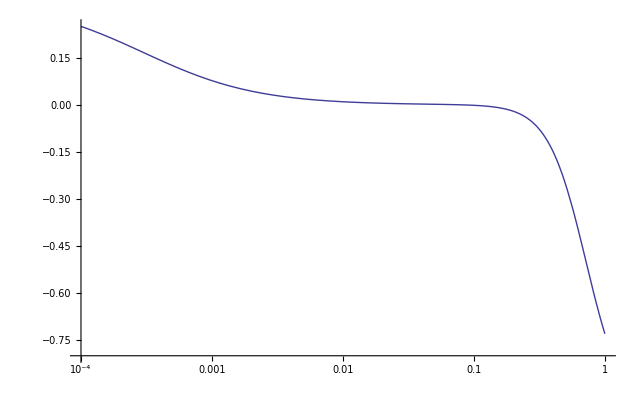

-194729.+3.56799×10^8 a^(1/9)-1.18914×10^9 a^(1/8)+1.55755×10^9 a^(1/7)-1.01651×10^9 a^(1/6)+3.45971×10^8 a^(1/5)-5.86945×10^7 a^(1/4)+4.31573×10^6 a^(1/3)-101465. √a+382.796 a

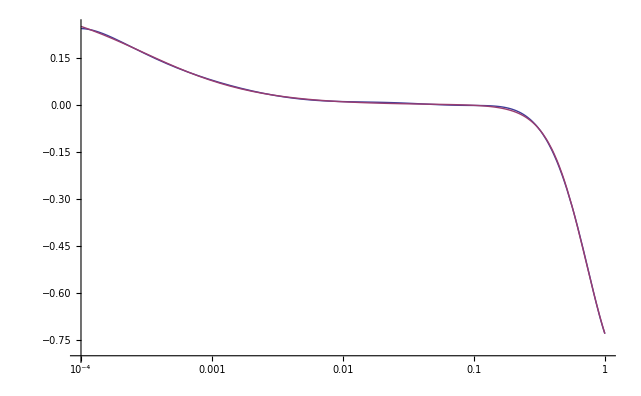

```mathematica
wleff[a_]=-1-2(a HL[a,H0,Ωm0,Ωr0,Ωx0] HL1[a,H0,Ωm0,Ωr0,Ωx0])/(3 HL[a,H0,Ωm0,Ωr0,Ωx0]^2)
LogLinearPlot[wleff[a],{a,10^-4,1},AxesOrigin-> {10^-4,-0.8}]
wlefff=Table[{aTable[[i]],wleff[aTable[[i]]]},{i,1,365}];
wlefffit[a_]=Fit[wlefff,{1,a,a^(1/2),a^(1/3),a^(1/4),a^(1/5),a^(1/6),a^(1/7),a^(1/8),a^(1/9)},a]
LogLinearPlot[{wlefffit[a],wleff[a]},{a,10^-4,1},AxesOrigin-> {10^-4,-0.8}]
```

```mathematica
H1[a_]=D[H[a]/.Sol[a][[1]][[1]],a];
H[a_]=H[a]/.Sol[a][[1]][[1]];
LogLogPlot[{H[a],Abs[H1[a]]},{a,10^-4,1}];
LogLogPlot[Abs[H1[a]],{a,10^-4,1}];
weff[xx_]=-1-2(H[1/xx] H1[1/xx])/(xx 3 H[1/xx]^2);
LogLinearPlot[weff[a],{a,10^-4,1}]
wefff=Table[{aTable[[i]],weff[aTable[[i]]]},{i,1,365}];
wefffit[xx_]=Fit[wefff,{1,xx,xx^2,xx^3,xx^4,xx^5},xx]
(*wefffit[a_]=Fit[wefff,{1,a^-1,a^(-1/2),a^(-1/3),a^(-1/4),a^(-1/5)},a]*)
LogLinearPlot[{wefffit[a],weff[a]},{a,10^-4,1}]
```

Part::partw: Part 1 of {} does not exist.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

General::ivar: -9.21034 is not a valid variable.

General::ivar: -9.02955 is not a valid variable.

General::ivar: -8.83356 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::ivar: -9.21015 is not a valid variable.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

General::ivar: -9.02219 is not a valid variable.

General::ivar: -8.83422 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::ivar: 1/xx is not a valid variable.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

General::ivar: 1/a is not a valid variable.

General::ivar: -0.108576 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

General::ivar: 10000. is not a valid variable.

General::ivar: 9090.91 is not a valid variable.

General::ivar: 8333.33 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

General::ivar: 10000. is not a valid variable.

General::ivar: 9090.91 is not a valid variable.

General::ivar: 8333.33 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

0.28152 xx^4 (9.71409 (-1-(6666.67 ∂_10000. Hold[H[1/0.0001]])/Hold[H[1/0.0001]])+9.70173 (-1-(6060.61 ∂_9090.91 Hold[H[1/0.00011]])/Hold[H[1/0.00011]])+9.68938 (-1-(«18» «1»«1»)/Hold[H[«1»]])+«498»)+0.215639 xx^2 (4.78441 (-1-(«18» ∂_(«1») «1»)/Hold[H[1/(«7»)]])+«488»)+«3»+0.251651 xx^3 («585»+140.096 (-1-(«19» «1»«1»)/Hold[H[1/(«3»)]]))

General::ivar: 1/a is not a valid variable.

General::ivar: 10000. is not a valid variable.

General::ivar: 9090.91 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

```mathematica
TTT[a_]=(-d2 (1/((3 H0^2/m^2(Ωm0 a^-3+Ωr0 a^-4)+2d1)^2))/(2d2 1/m^2 1/((3 H0^2/m^2(Ωm0 a^-3+Ωr0 a^-4)+2d1)^3))-3 H0^2(Ωm0 a^-3+Ωr0 a^-4)-2d1 m^2)a^2
TTT[10^-3]
TTT[10^-2]
TTT[10^-1]
TTT[1]
```

(-44159.2-680.535 (32.4444+11.1111 (0.0000809/a^4+0.27/a^3))-15123. (0.0000809/a^4+0.27/a^3)) a^2

-7.95999×10^6

-630840.

-62094.1

-72365.4